## Optimal control of a two-level system (Problem 13.5) adapted from d’Alessandro, Chapter 6.3 (and exercise 6.2)

```mathematica
Clear["Global`*"];
```

Define Pauli matrices

```mathematica
Subscript[σ, 1]=({{0, 1}, {1, 0}});  Subscript[σ, 2]=({{0, -ⅈ}, {ⅈ, 0}});  Subscript[σ, 3]=({{1, 0}, {0, -1}});
```

Check commutation relations

```mathematica
f[a_,b_]:=a.b-b.a  (* define the commutator *)
```

```mathematica
{f[Subscript[σ, 1],Subscript[σ, 2]]//MatrixForm,f[Subscript[σ, 2],Subscript[σ, 3]]//MatrixForm,f[Subscript[σ, 3],Subscript[σ, 1]]//MatrixForm}
```

{(2 ⅈ | 0
0 | -2 ⅈ),(0 | 2 ⅈ
2 ⅈ | 0),(0 | 2
-2 | 0)}

```mathematica
{f[Subscript[σ, 1],Subscript[σ, 2]]==2ⅈ Subscript[σ, 3],f[Subscript[σ, 2],Subscript[σ, 3]]==2ⅈ Subscript[σ, 1],f[Subscript[σ, 3],Subscript[σ, 1]]==2ⅈ Subscript[σ, 2]}
```

{True,True,True}

Define 4x4 matrices for real representation

```mathematica
z2=({{0, 0}, {0, 0}});Subscript[T, 1]=1/2({{z2, -Subscript[σ, 1]}, {Subscript[σ, 1], z2}})//ArrayFlatten; Subscript[T, 2]=1/2({{-ⅈ Subscript[σ, 2], z2}, {z2, -ⅈ Subscript[σ, 2]}})//ArrayFlatten;Subscript[T, 3]=1/2({{z2, -Subscript[σ, 3]}, {Subscript[σ, 3], z2}})//ArrayFlatten;

 {MatrixForm[Subscript[T, 1]],MatrixForm[Subscript[T, 2]],MatrixForm[Subscript[T, 3]]}
```

{(0 | 0 | 0 | -1/2
0 | 0 | -1/2 | 0
0 | 1/2 | 0 | 0
1/2 | 0 | 0 | 0),(0 | -1/2 | 0 | 0
1/2 | 0 | 0 | 0
0 | 0 | 0 | -1/2
0 | 0 | 1/2 | 0),(0 | 0 | -1/2 | 0
0 | 0 | 0 | 1/2
1/2 | 0 | 0 | 0
0 | -1/2 | 0 | 0)}

```mathematica
{f[Subscript[T, 1],Subscript[T, 2]]==Subscript[T, 3],f[Subscript[T, 2],Subscript[T, 3]]==Subscript[T, 1],f[Subscript[T, 3],Subscript[T, 1]]==Subscript[T, 2]}
```

{True,True,True}

Minimize the cost function  j

```mathematica
α=√((ω0+ω)^2+(ω1)^2);  j =1-(ω1/α Sin[1/2 α T])^2+ η (ω1)^2 T;
D[α, ω]//FullSimplify
```

(ω+ω0)/(√((ω+ω0)^2+ω1^2))

```mathematica
{j1=j/.{ω->-ω0},j1//FullSimplify,j2=1/2(1+Cos [θ] + η θ^2)}
```

{1+T η ω1^2-Sin[(T √(ω1^2))/2]^2,1/2 (1+2 T η ω1^2+Cos[T ω1]),1/2 (1+η θ^2+Cos[θ])}

```mathematica
p1=Plot[j2/.η->{0,0.2,0.5,1},{θ,0,1.5π},PlotRange->{0,2}];
```

```mathematica
{dj2dθ = D[j2, θ]//Simplify,η1=Solve[dj2dθ==0,η],j2/.η1}
```

{η θ-Sin[θ]/2,{{η→Sin[θ]/(2 θ)}},{1/2 (1+Cos[θ]+1/2 θ Sin[θ])}}

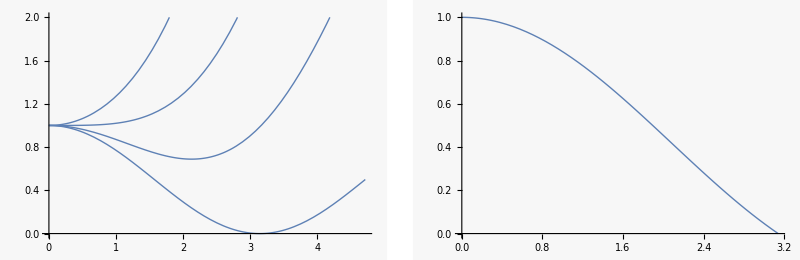

```mathematica
p2=Plot[Sinc[θ],{θ,0,π}];
GraphicsRow[{p1,p2}]
```